```mathematica
dataSemantic=SemanticImport[(*Insert the file path for Data A0 here*)"/Users/tante/Workspaces_UZH/mathematica/DATA_A0.csv",
<|2-> String,3-> Integer,5-> String,6-> String,7-> Integer,8-> Integer,13-> Integer,14->Integer,15-> Integer,17->String,19-> String,21-> String, 23-> String,24->Integer,26->Integer, 27-> Integer,28->Integer,30->Integer|> ];
dataA0=Dataset@dataSemantic;
dataA0
```

Dataset[<>]

```mathematica
Max[dataA0[[All, "age"]]]
```

22

```mathematica
dataA0[455, "Dalc"]
```

1

```mathematica
Length[dataA0[Select[#Dalc == 5&]]]
```

17

```mathematica
Length[dataA0[Select[#Walc == _Missing&]]]
```

0

```mathematica
dataA0[Count[_Missing], "Walc"]
```

0

```mathematica
dataA01=dataA0[All,Append[#,"tc"->N[#Dalc/2+#Walc/2]]&];
```

```mathematica
ageTc=dataA01[[All,{"age","tc"}]][[All, Values]]
```

Dataset[<>]

```mathematica
model=LinearModelFit[Normal[ageTc],x,x, ConfidenceLevel->0.99]
```

FittedModel[0.272438+0.0966861 x]

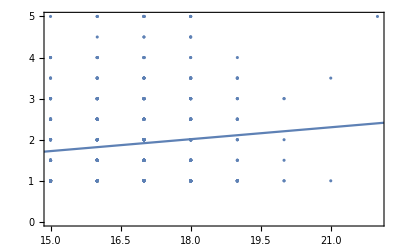

```mathematica
Show[ListPlot[Normal[ageTc]],Plot[model[x],{x,10,25}],Frame->True]
```

```mathematica
model["AdjustedRSquared"]
```

0.0124533

```mathematica
model[20]
```

2.20616

```mathematica
model["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | 0.272438 | 0.535986 | {-1.11225,1.65713}
x | 0.0966861 | 0.031926 | {0.014207,0.179165}

```mathematica
dataA01 = dataA01/.{"M"-> 0, "F"-> 1}
```

Dataset[<>]

```mathematica
model2 = LinearModelFit[Normal[dataA01[[All,{"sex","age","studytime","goout", "tc"}]][All, Values]],{x1,x2,x3,x4},{x1,x2,x3,x4}]
```

FittedModel[0.353223-0.605729 x1+0.0763474 x2-0.138339 x3+0.27766 x4]

```mathematica
model2[1,20,1,5]
```

2.52441

```mathematica
Dataset[<>]
```